```mathematica
Clear[enhancedGRN3];
enhancedGRN3[k1tx_,k1ctx_,Gtot_:10,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,G1,T1,R1,G1c,T1c,C1,sol,rsys,G1f,R1G1f},
rsys={
(* Genelet R1 *)
rxn[G1,G1+T1,k1tx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Genelet C1 *)
rxn[G1c,G1c+T1c,k1ctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+G1f,R1G1f,kf,kr],

conc[G1,1],
conc[G1c,1],
conc[G1f,Gtot]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{G1f[t]}/.sol]
]

tmax=60;
k1ctx=5;

y=Table[{i,enhancedGRN3[i,k1ctx,10,1.5,0.05,tmax][[1]][[0]][tmax]},{i,k1ctx-5,k1ctx+5,0.1}];
inv=Interpolation[y];
```

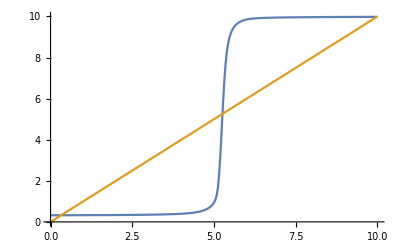

```mathematica
Plot[{inv[inv[x]],x},{x,0,10}]
```

Note that this gets more and more crisp with a longer sequence (just as in the dimerizing example).

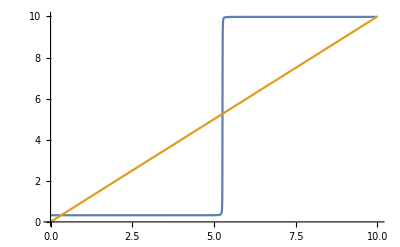

```mathematica
Plot[{inv[inv[inv[inv[x]]]],x},{x,0,10}]
```

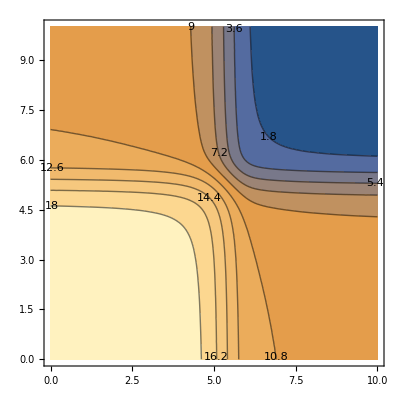

```mathematica
NAND[x_,y_]:=inv[x]+inv[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->10]
```

More like a NOT gate...
How about if I change the contours?

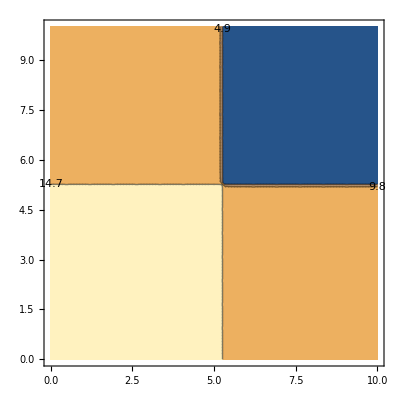

```mathematica
strongNOT[x_]:=inv[inv[inv[x]]]
NAND[x_,y_]:=strongNOT[x]+strongNOT[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->3]
```

Haha...not really (what does this mean? A gate that’s really good at distinguishing between bits that are of the same parity, and bits that are not?)

Actually if we just pick the right contours, it’ll be good.

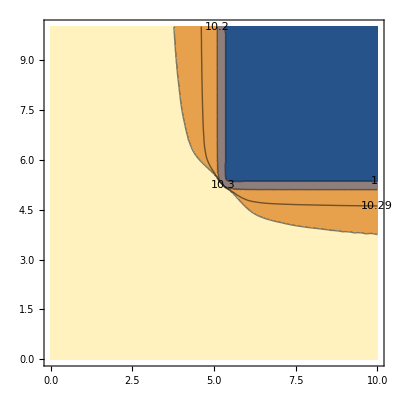

```mathematica
strongNOT[x_]:=inv[inv[inv[x]]]
NAND[x_,y_]:=strongNOT[x]+strongNOT[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->{1,10.29,10.30,10.2}]
```

Can we achieve the same results, by changing the simulation parameters?

```mathematica
k1ctx=8;
y=Table[{i,enhancedGRN3[i,k1ctx,10,1.0,0.05,tmax][[1]][[0]][tmax]},{i,0,10,0.1}];
inv=Interpolation[y];
```

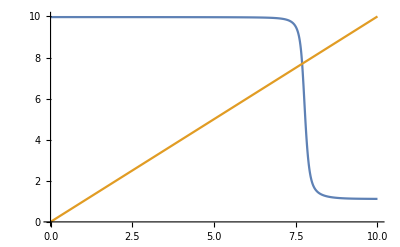

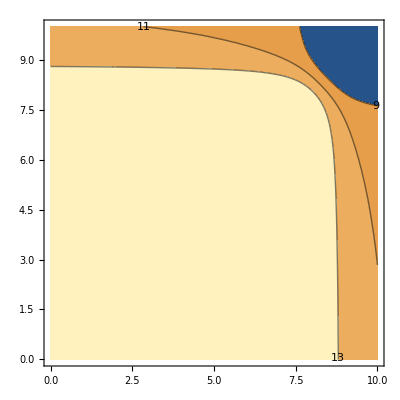

```mathematica
Plot[{inv[inv[inv[x]]],x},{x,0,10}]
NAND[x_,y_]:=inv[x]+inv[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->{9,11,13}]
```

Now I have to figure out to make the gates a function of concentration, as oppposed to rate constants...
This will likely require me to introduce transcription factors into my system.

```mathematica
Clear[enhancedGRN4];
enhancedGRN4[Rconc_,Cconc_,k1_:1.0,ktx_:500.0,kON_:100.0,kOFF_:25,tot_:10,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,r,c,rG1,cG1c,G1,G1c,T1,T1c,R1,C1,sol,rsys,OFF,ON},
rsys={
(* Gene R1 *)
revrxn[r+G1,rG1,k1,k1],
rxn[rG1,rG1+T1,ktx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Gene C1 *)
revrxn[c+G1c,cG1c,k1,k1],
rxn[cG1c,cG1c+T1c,ktx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+OFF,ON,kON,kOFF],

conc[r,Rconc],
conc[c,Cconc],
conc[G1,1],
conc[G1c,1],
conc[OFF,tot]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{ON[t]}/.sol]
]

(*plotter=enhancedGRN4[0,5];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"ON" ]*)
enhancedGRN4Plot[r_,c_]:=(
plotter=enhancedGRN4[r,c];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"G1f" ])

(* Above the threshold, so manipulating kf will be of particular interest *)
Manipulate[enhancedGRN4Plot[a,5],{a,0,10}]
```

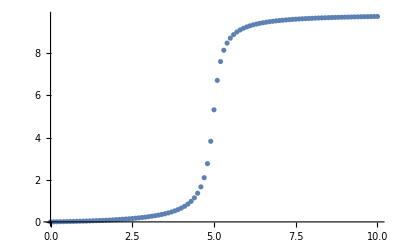

```mathematica
tmax=60;
c=5;

y=Table[{i,enhancedGRN4[i,c][[1]][[0]][tmax]},{i,0,10,0.1}];
ListPlot[y]
```

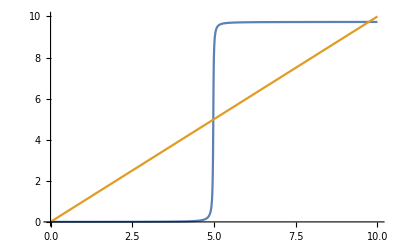

```mathematica
inv2=Interpolation[y];
Plot[{inv2[inv2[x]],x},{x,0,10}]
```

OK - this works as desired.

Now, the next step is to build composable circuits.

{InterpolatingFunction[{{0., 50.}}, <>][t]}

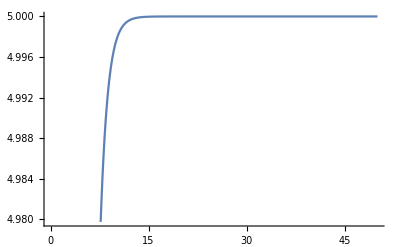

```mathematica
titrantGRN[]:=Module[{G1c,T1c,C1,null},
(* Gene C1 *)
ktx=5.0;
ktl=krd=kpd=1.0;
tmax=50;
rsys={
rxn[G1c,G1c+T1c,ktx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

conc[G1c,1]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{C1[t]}/.sol]
]
plotter=titrantGRN[]
Plot[plotter,{t,0,50}]
```

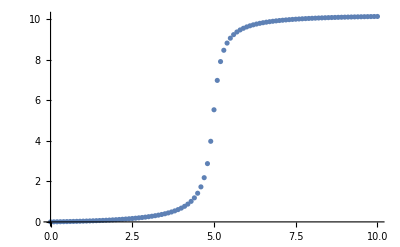

```mathematica
Clear[enhancedGRN5];
enhancedGRN5[Rconc_,Cconc_,k1_:1.0,ktx_:500.0,kON_:100.0,kOFF_:25,tot_:10,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0,kftx_:5.2]:=
Module[{null,r,c,rG1,cG1c,G1,G1c,T1,T1c,R1,C1,sol,rsys,OFF,ON,T,OUT},
rsys={
(* Gene R1 *)
revrxn[r+G1,rG1,k1,k1],
rxn[rG1,rG1+T1,ktx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Titrant Gene C1 *)
revrxn[c+G1c,cG1c,k1,k1],
rxn[cG1c,cG1c+T1c,ktx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+OFF,ON,kON,kOFF],
rxn[ON,ON+T,kftx],
rxn[T,T+OUT,ktl],
rxn[T,null,krd],
rxn[OUT,null,kpd],

conc[r,Rconc],
conc[c,Cconc],
conc[G1,1],
conc[G1c,1],
conc[OFF,tot]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{OUT[t]}/.sol]
]
plotter=enhancedGRN5[2,5];
enhancedGRN5Plot[r_,c_]:=(
plotter=enhancedGRN5[r,c];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"G1f" ])

tmax=60;
c=5;

Manipulate[enhancedGRN5Plot[a,5],{a,0,10}]
y=Table[{i,enhancedGRN5[i,c][[1]][[0]][tmax]},{i,0,10,0.1}];
ListPlot[y]
```

```mathematica
SS[k1tx_,k1ctx_,Gtot_: 10,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=(
epsilon=0.05;
plot=enhancedGRN3[k1tx,k1ctx,Gtot,kf,kr,tmax,kc,ktl,kpd,krd][[1]][[0]];
If[k1tx>k1ctx,
Return[Max[plot[tmax],epsilon*Gtot]],
Return[Min[plot[tmax],(1-epsilon)*Gtot]]]
)
```

{InterpolatingFunction[{{0., 100.}}, <>][t]}

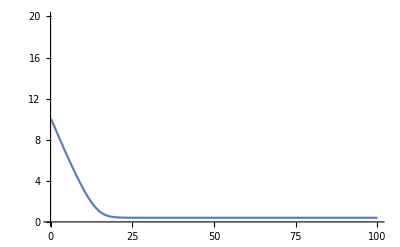

InterpolatingFunction[{{0., 100.}}, <>]

InverseFunction[InterpolatingFunction[{{0., 100.}}, <>]]

1.55966

0.5

```mathematica
Clear[test];
test=enhancedGRN3[9,5,10,1.5,0.05,100]
Plot[test,{t,0,100},PlotRange->{0,20}]
test=test[[1]][[0]]
x=InverseFunction[test]
test[1];
x[9]

SS[9,5,10,1.5,0.05,100]
```